# Supplementary tensors

## ITensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ITensor`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.040673,Null}

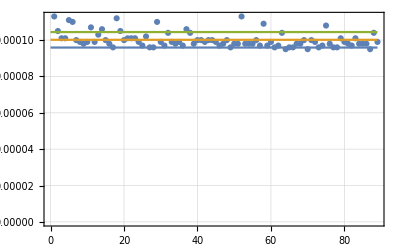

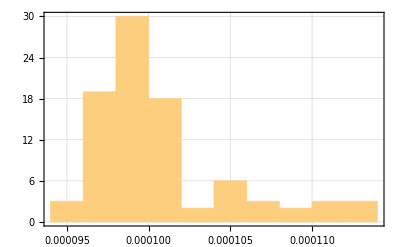

{0.0000958962,0.000100157,0.000104418}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[2]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.074542,Null}

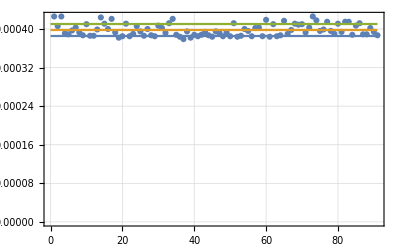

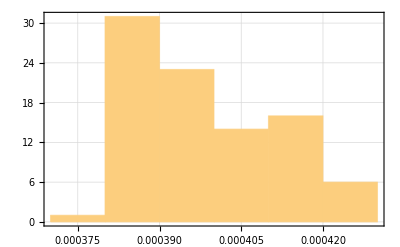

{0.000385484,0.000397912,0.00041034}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[3]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.576855,Null}

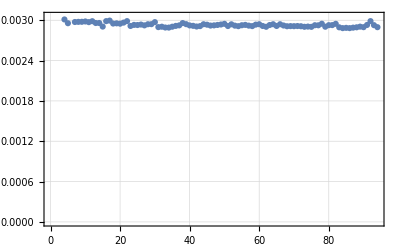

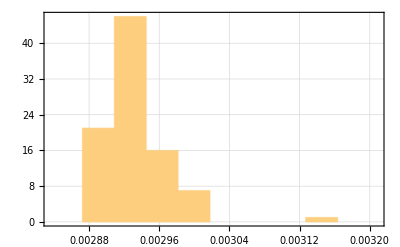

{-0.00124327,0.00382929,0.00890184}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[4]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{4.24109,Null}

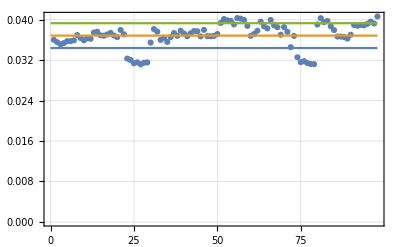

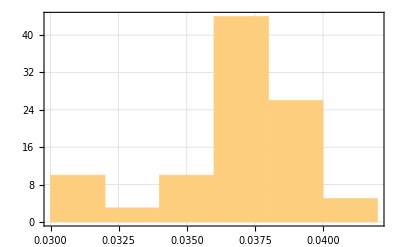

{0.0344111,0.0368676,0.0393242}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[5]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CTensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.10354,Null}

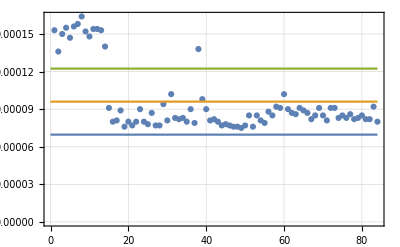

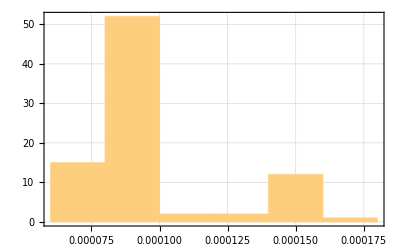

{0.0000696545,0.0000960119,0.000122369}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.126117,Null}

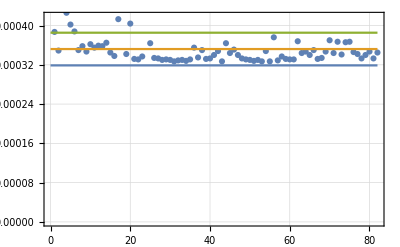

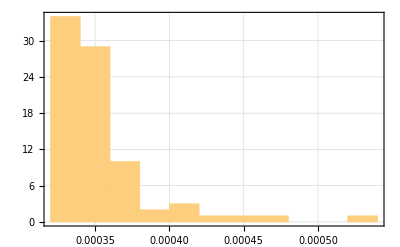

{0.000318823,0.00035211,0.000385396}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.453799,Null}

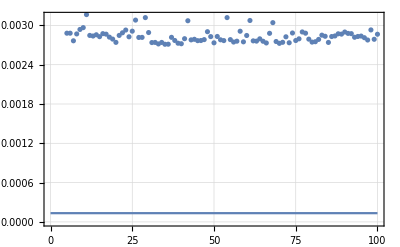

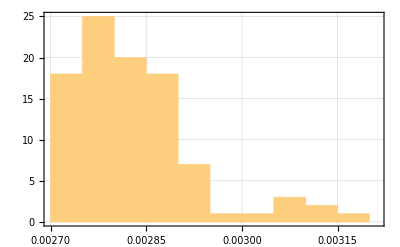

{0.000133311,0.00339442,0.00665553}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{4.05804,Null}

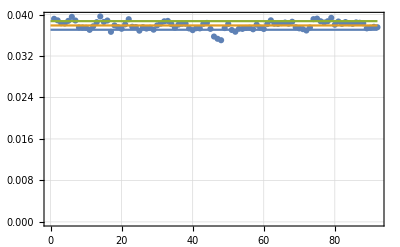

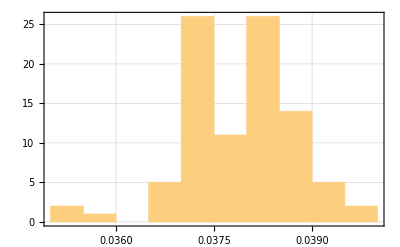

{0.0370632,0.0378944,0.0387256}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{76.1207,Null}

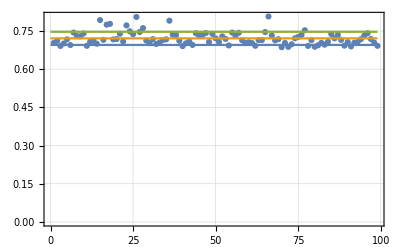

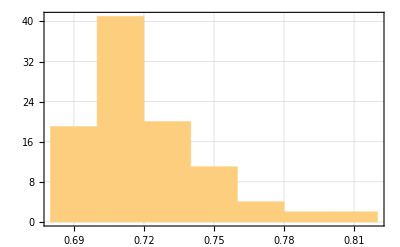

{0.695171,0.721014,0.746856}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C1Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.085694,Null}

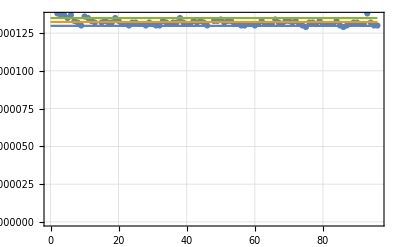

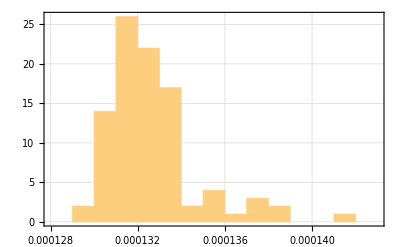

{0.000129781,0.000132365,0.000134948}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.148097,Null}

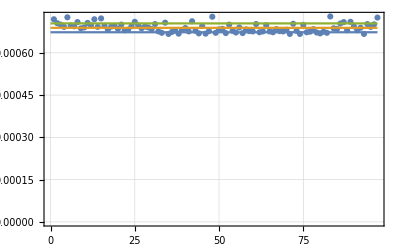

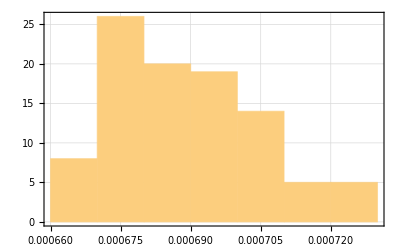

{0.000672942,0.000688639,0.000704336}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.831226,Null}

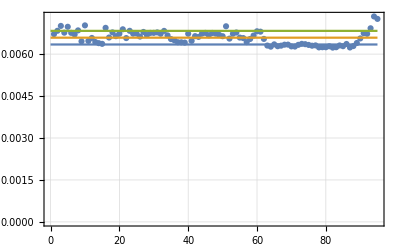

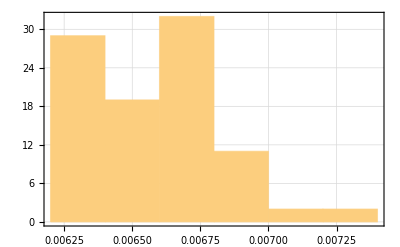

{0.00634348,0.00658702,0.00683056}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{10.3068,Null}

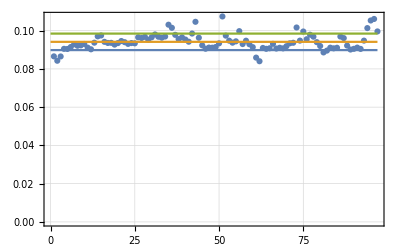

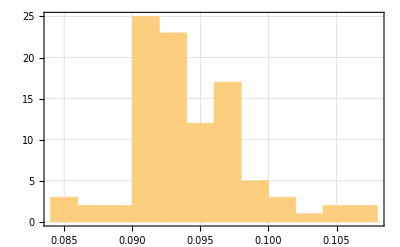

{0.0898411,0.0941549,0.0984688}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{290.705,Null}

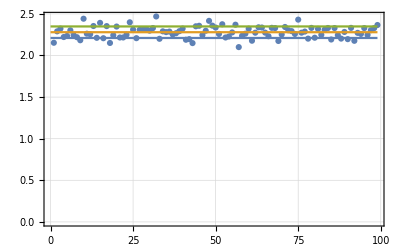

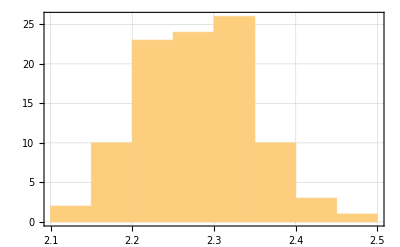

{2.2106,2.27992,2.34925}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C2Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.094836,Null}

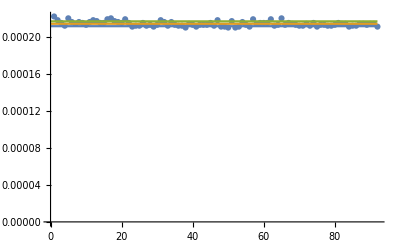

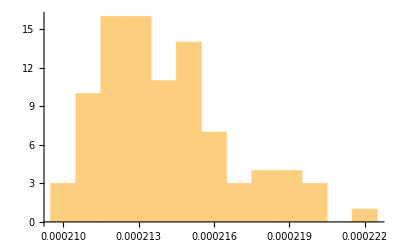

{0.000211483,0.000214098,0.000216712}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.221866,Null}

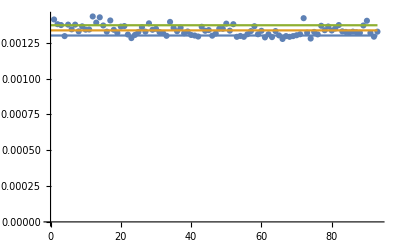

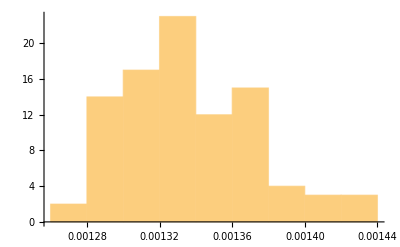

{0.00130011,0.0013359,0.00137169}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.63875,Null}

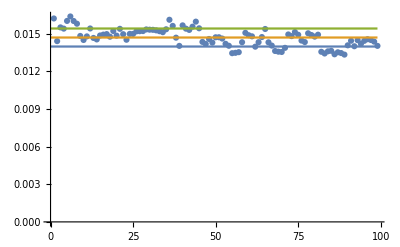

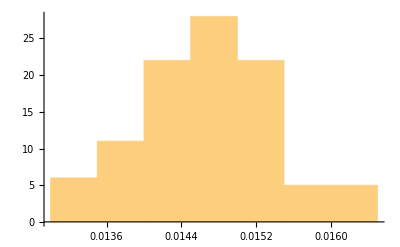

{0.0139719,0.0146897,0.0154075}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{122.907,Null}

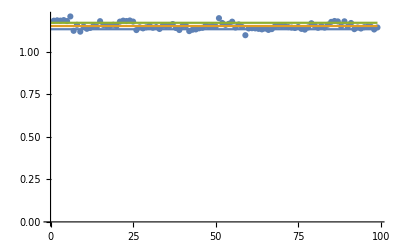

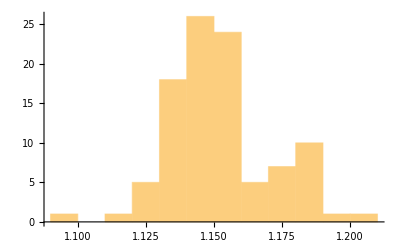

{1.13317,1.15206,1.17095}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{586.613,Null}

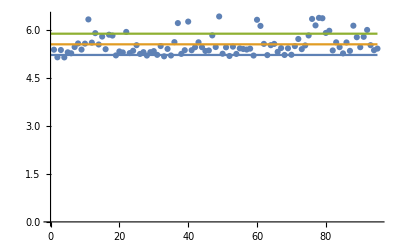

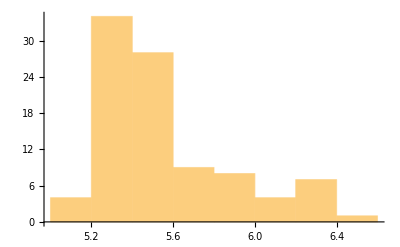

{5.222,5.55461,5.88722}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CTensors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.355423,Null}

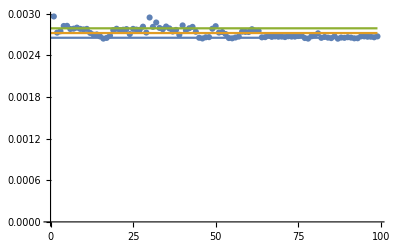

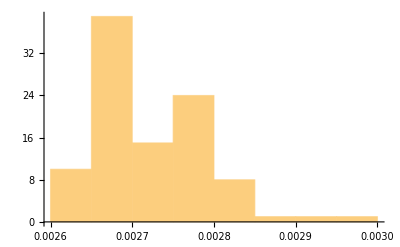

{0.00265294,0.00272108,0.00278922}

```mathematica
theData1 = {};
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{0.752528,Null}

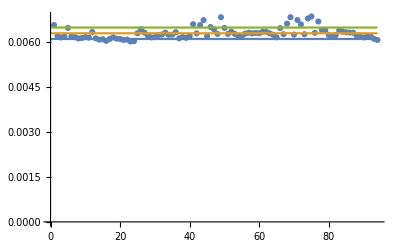

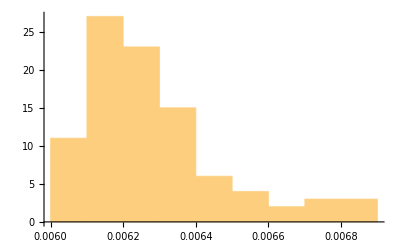

{0.00609126,0.0062813,0.00647133}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{1.85226,Null}

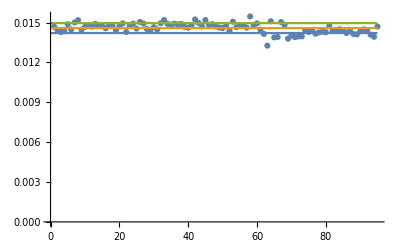

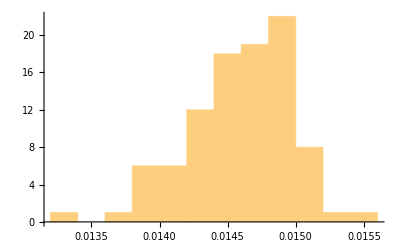

{0.014216,0.0145895,0.014963}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{3.37041,Null}

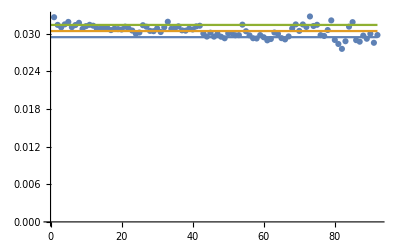

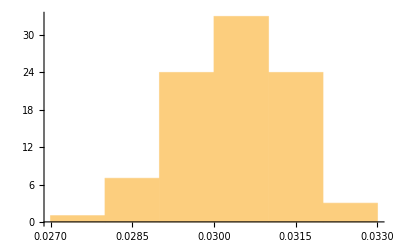

{0.0294186,0.0303923,0.0313661}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{45.3601,Null}

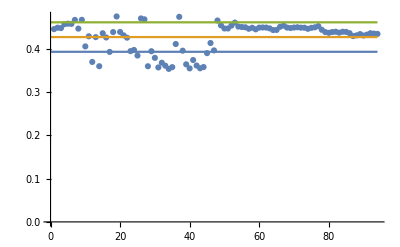

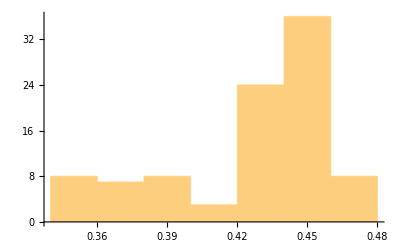

{0.393078,0.427137,0.461196}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{67.7119,Null}

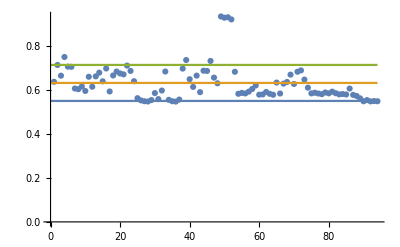

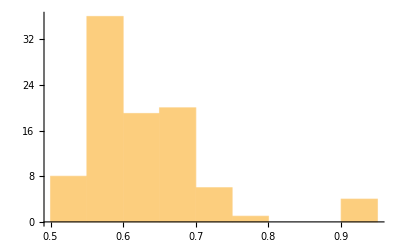

{0.550408,0.632324,0.714239}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

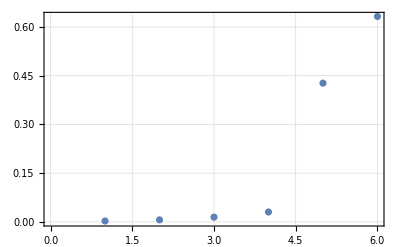

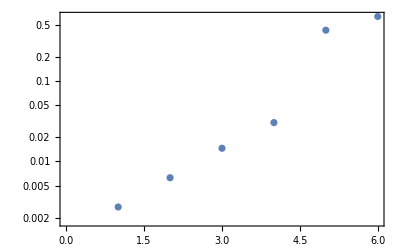

```mathematica
ListPlot[theData1,PlotTheme->"Detailed"]
ListLogPlot[theData1,PlotTheme->"Detailed"]
```

```mathematica
NotebookSave[]
```

# Scalar-graviton vertices

## Kinetic term

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.576448,Null}

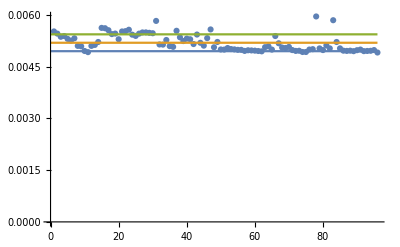

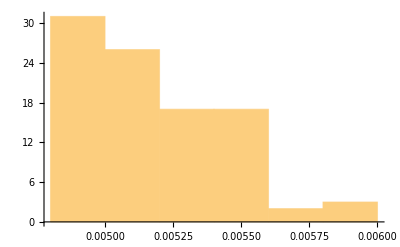

{0.00494849,0.00519256,0.00543664}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[1],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{2.20308,Null}

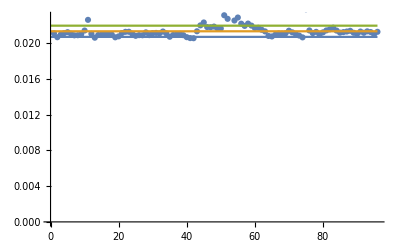

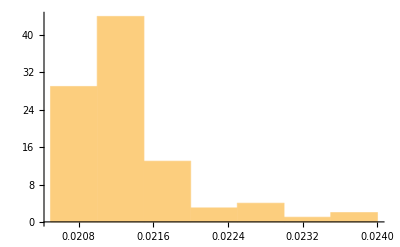

{0.0207105,0.0213383,0.021966}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[2],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{19.8895,Null}

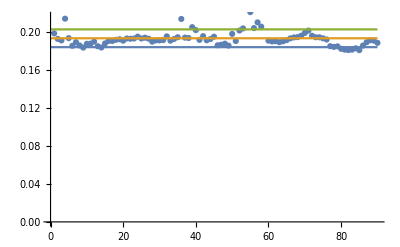

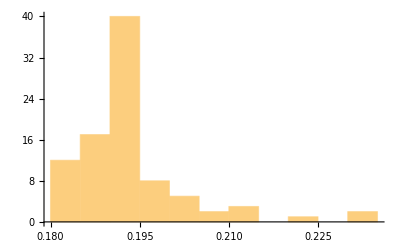

{0.183924,0.193282,0.202639}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[3],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Potential term

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.049902,Null}

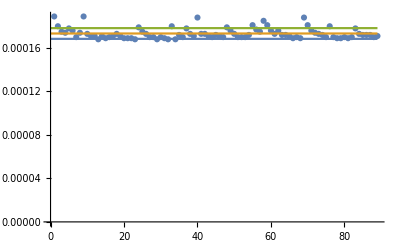

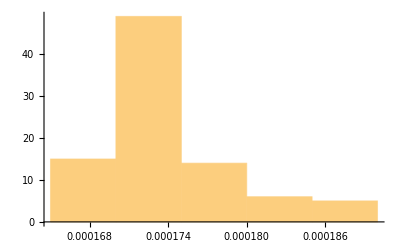

{0.000168388,0.000173326,0.000178264}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[1],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.067227,Null}

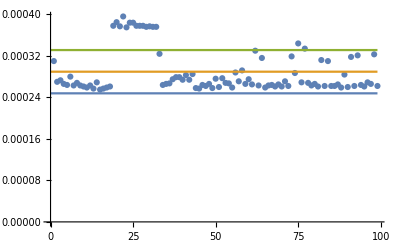

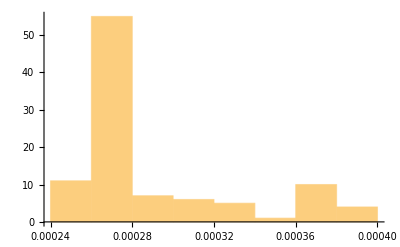

{0.000247816,0.000289525,0.000331234}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[2],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.102959,Null}

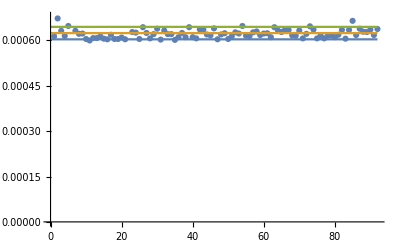

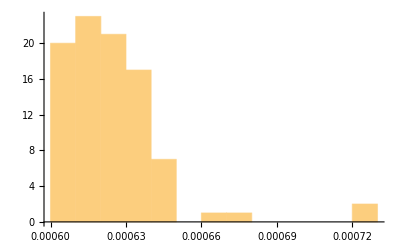

{0.000603838,0.000624467,0.000645097}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[3],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton-fermion vertex

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonFermionVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.535343,Null}

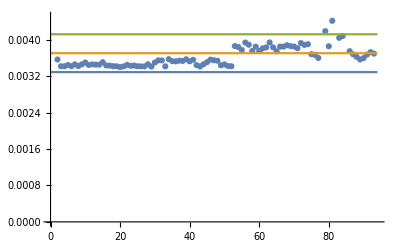

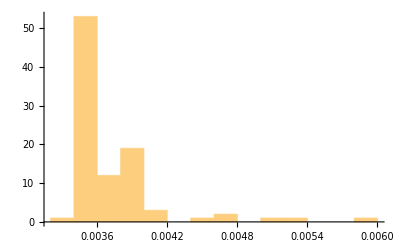

{0.00328597,0.0037013,0.00411663}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[1],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{2.09279,Null}

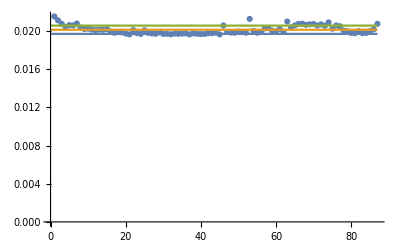

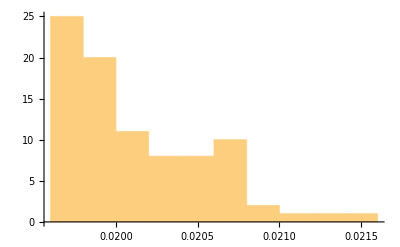

{0.0196973,0.0201302,0.020563}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[2],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{21.271,Null}

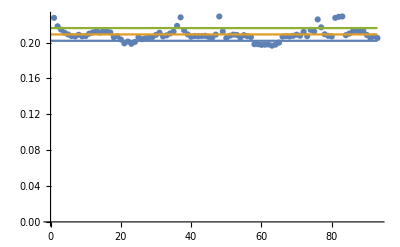

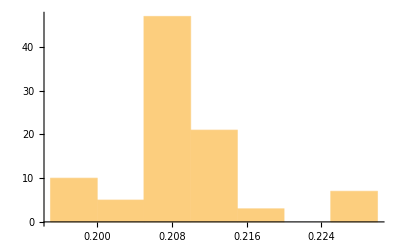

{0.202011,0.209103,0.216194}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[3],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton-vector vertices

## Massive vectors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{2.69415,Null}

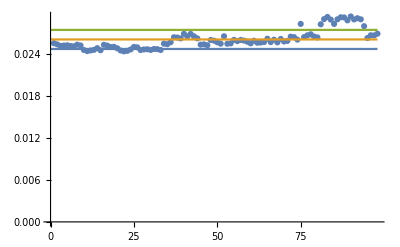

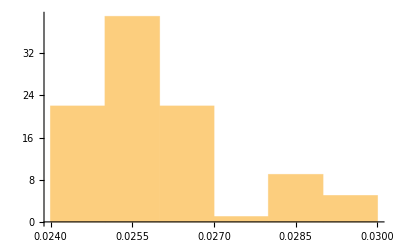

{0.0246659,0.026025,0.0273842}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[1],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{25.1066,Null}

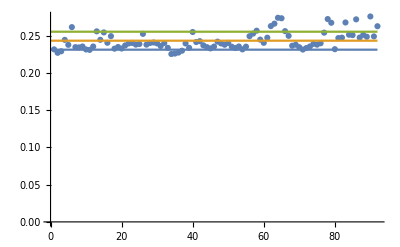

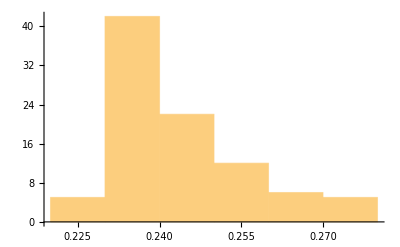

{0.231465,0.24354,0.255615}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[2],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{335.327,Null}

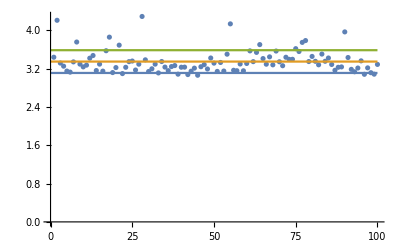

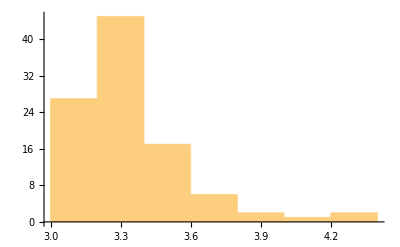

{3.11245,3.3504,3.58834}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[3],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Massless vectors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{4.546,Null}

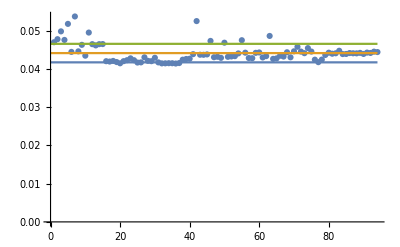

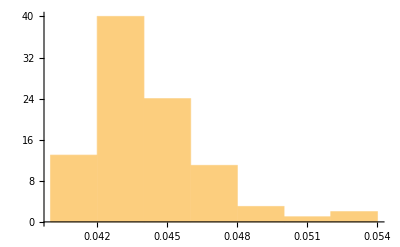

{0.0417258,0.0441453,0.0465648}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[1],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{62.441,Null}

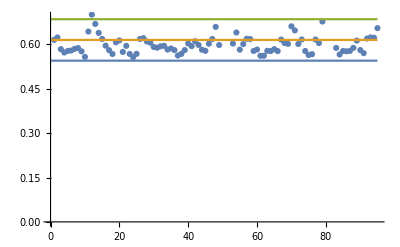

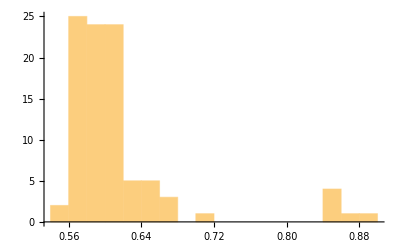

{0.545026,0.615131,0.685237}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[2],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[3],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Ghosts

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.362873,Null}

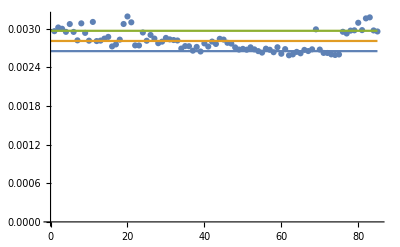

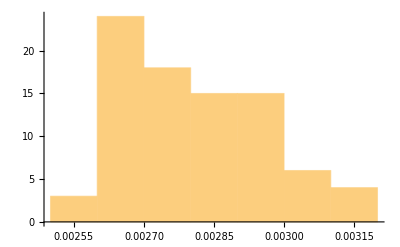

{0.00265066,0.00280848,0.00296631}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorGhostVertex[DummyArray[1],p1,p2]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorGhostVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.88871,Null}

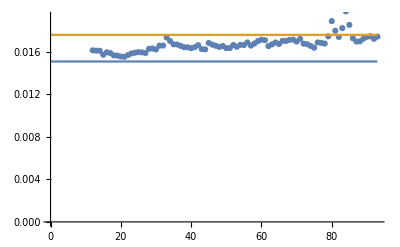

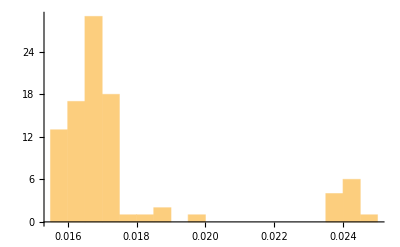

{0.0150827,0.0175866,0.0200905}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorGhostVertex[DummyArray[2],p1,p2]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorGhostVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{17.4075,Null}

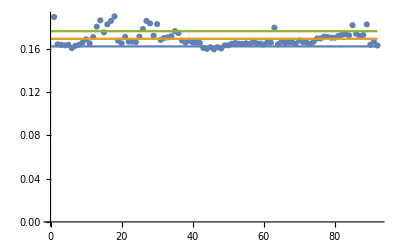

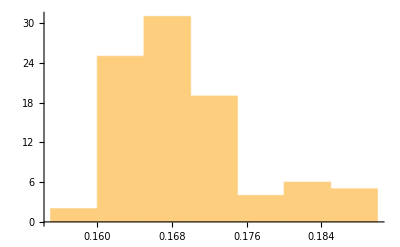

{0.162189,0.16921,0.176231}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorGhostVertex[DummyArray[3],p1,p2]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorGhostVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton vertices

## Pure graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{14.9892,Null}

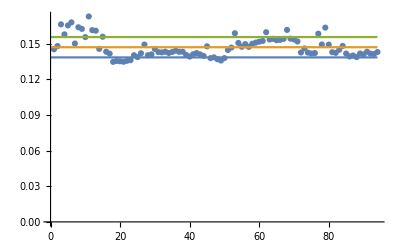

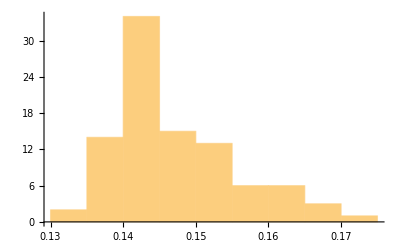

{0.138511,0.14708,0.155649}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonVertex[DummyArrayK[2],ε]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{673.137,Null}

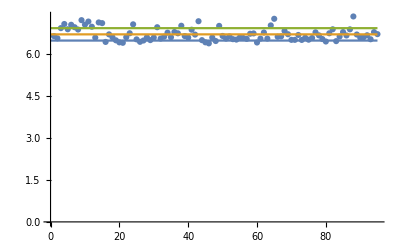

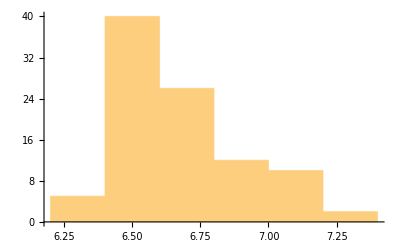

{6.46179,6.6829,6.904}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonVertex[DummyArrayK[3],ε]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Graviton-ghost vertex

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{4.83899,Null}

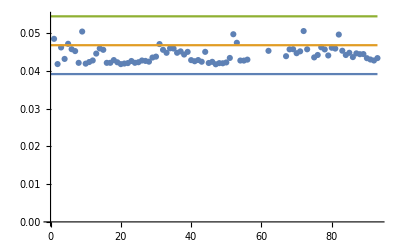

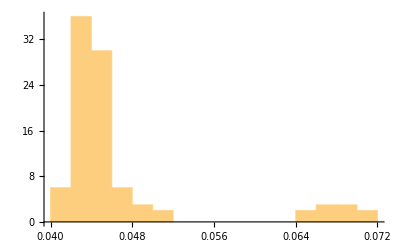

{0.0391109,0.0467495,0.0543881}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonGhostVertex[DummyArrayK[1],μ,p1,ν,p2]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{99.2485,Null}

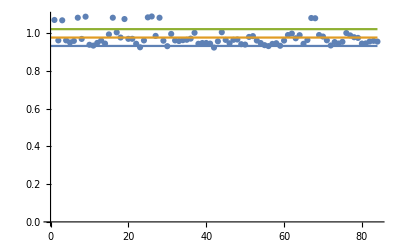

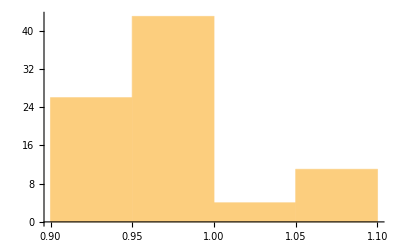

{0.932293,0.976816,1.02134}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonGhostVertex[DummyArrayK[2],μ,p1,ν,p2]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1887.93,Null}

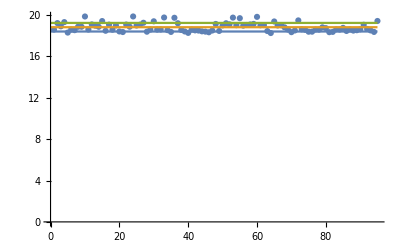

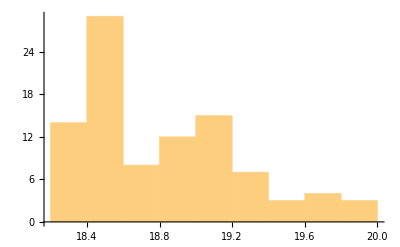

{18.4073,18.8225,19.2378}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonGhostVertex[DummyArrayK[3],μ,p1,ν,p2]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```